Adapted from Jiwon Yun’s notebook, "entropy"

## Preliminary

```mathematica
(* SetDirectory["~/projects/mcfgcky2_repos/"]; *) (* John's laptop *)
SetDirectory[NotebookDirectory[]];
```

```mathematica
Off[Graph::optx];  (* Turn off warnings about graph options *)
```

```mathematica
<<Combinatorica` (* was <<DiscreteMath`Combinatorica`;  *)
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionaliy. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

I increased WorkingPrecision in CalculateZ to avoid rounding off some very small Z values to zero, which was happening in the 6th sentence of the K-H stimuli. Turn off the complaining about how that FindRoot call is using arguments with lower precision than that. Also turn off warnings about line search.

```mathematica
Off[FindRoot::precw]; Off[FindRoot::bddir]
```

## Normalize Grammar

note that this function does not divide by the sum of the weights of rules sharing the same LHS; rather it preserves the given weight as a Mathematica fraction. This is key for deriving Z values other than 1.

```mathematica
ChartToGrammar[ch_,startsymbolregexp_ :"S.*"] := Module[{nonterminals,terminals},
LhsRhsSymbol[line_] :=Switch[Length[line],
6, {Part[line,4],Part[line,6]},   (* terminal line *)
7,{Part[line,4],Part[line,6]},    (* unary with string rewriting recipe *)
8,{Part[line,4],Part[line,6],Part[line,7]}, (* binary *)
_,{}];

LhsSymbol[line_] :=Switch[Length[line],
6, {Part[line,4]},
7,{Part[line,4]},
8,{Part[line,4]},
_,{}];

kind[f_] := DeleteDuplicates[Flatten[f /@ ch ]];

nonterminals = kind[LhsSymbol];
terminals = Complement[kind[LhsRhsSymbol],kind[LhsSymbol]];
(* both = Join[nonterminals,terminals]; *)

markup[line_] :=Switch[Length[line], (* throw away recipe *)
6, {"Preterminal",Part[line,1]/Part[line,3],Part[line,4],Part[line,6]},
7,{"Unary",Part[line,1]/Part[line,3],Part[line,4],Part[line,6]},
8,{"Binary",Part[line,1]/Part[line,3],Part[line,4],Part[line,6],Part[line,7]}, 
_,{}];
Return[{ First[Select[nonterminals,StringMatchQ[#,RegularExpression[startsymbolregexp]]&]],(* assume it's the first one *)
              nonterminals,   (* second and third components constitute a disjoint set of vertex labels *)
              terminals,
		markup/@ch (* was : divide /@ vulgar *)
	}]
];
```

## Create Graph Projection

```mathematica
GraphProjection[g_ ]:= Module[{start,nonterminals,terminals,vertices,rules,edges,i},
	{start,nonterminals,terminals,rules} =g;
	vertices = Join[nonterminals,terminals];
	edges ={};
	
	lookup[rulenum_,eltnum_] := FromDigits[FromDigits[Position[vertices,rules[[rulenum]][[eltnum]]]]];

	For[i=1,i≤ Length[rules],i++,
	    Switch[First[rules[[i]]],
	 "Preterminal",AppendTo[edges,{lookup[i,3],lookup[i,4]}],
	"Unary",AppendTo[edges,{lookup[i,3],lookup[i,4]}],
	"Binary",AppendTo[edges,{lookup[i,3],lookup[i,4]}];
			   AppendTo[edges,{lookup[i,3],lookup[i,5]}]
	]
	];

Return[FromOrderedPairs[edges]]
];
```

## Strongly - Connected Components

Whereas Cormen, Leisersohn and Rivest give just one, more complicated function, I split things up into two different DFS functions. One records finishing times while the other keeps track of "depth first forests" originating from a given start point. Node numbers for vertices in these forests are stored on the lastfound list

```mathematica
ftimeDFSVisit[u_Integer] :=
		Module [{}, (* recursive helper function for ftimeDFS, below *)
		color[[u]] = Gray;
			Scan[ (If[color[[#]]==White,
				ftimeDFSVisit[#];
				color[[u]]=Black];
				   t++;
			   ftime[[u]]= t;
		)&,e[[u]]
			]
		]
```

```mathematica
ftimeDFS[g_Graph] := (* this function computes a list of finishing times in a DFS traversal of g. p541 of Cormen, Leisersohn & Rivest *)
	Block[{color=Table[White,{V[g]}],t=0,e=ToAdjacencyLists[g],ftime=Table[-1,{V[g]}],$RecursionLimit = Infinity},
	(* for each vertex, check if we've been there before, otherwise call ftimeDFSVisit *)
	Do[If[color[[vert]]==White,ftimeDFSVisit[vert]],{vert,1,V[g]}];
	
	Return[Sort[Range[1,V[g]],(ftime[[#1]]>ftime[[#2]])&]] (* Descending order order on times = Ascending whole numbers *)
	]
```

```mathematica
myDFSVisit[u_Integer] := Module [{}, (* recursive helper function for myDFS, below *)
	AppendTo[lastfound,u];
	color[[u]] = Gray;
	Scan[ (If[color[[#]]==White,
			myDFSVisit[#];
			color[[u]]=Black])&,e[[u]]
		]
]
```

```mathematica
myDFS[graph_Graph,orderedvertices_List] := (* same algorithm but keep track of all vertices in what CLR call the Depth-first Forest *)
	Block[{color=Table[White,{V[graph]}],e=ToAdjacencyLists[graph],lastfound={},$RecursionLimit = Infinity},
	(If[color[[#]]== White,myDFSVisit[#];AppendTo[SCCs,lastfound];lastfound={}])& /@ orderedvertices
	]
```

```mathematica
getSCCs[graph_Graph] := 
Block[{SCCs={}},
	myDFS[ReverseEdges[graph],ftimeDFS[graph]];
	Return[Reverse[SCCs]]
	]
```

## Calculate Inside Probabilities

page 146 of Nederhof & Satta (2008) Computing Partition Functions of PCFG

```mathematica
CalculateZ[grammar_,graphprojection_,sortedSCCs_] := Module[{myZ,start,nonterminals,terminals,rules,tbl,vertices,vertexNumber,vertexLabel,eqns,vars,zValues},
{start,nonterminals,terminals,rules} =grammar;
vertices = Join[nonterminals,terminals]; (* this is the ordering used in GraphProjection *)

(* lookup table maps from a given nonterminal number to all the rules sharing that nonterminal *)
tbl = Function[nt,Select[rules,Part[#,3]==nt&]]/@ nonterminals;

(* Initialize the list of Z values as 0 *)
myZ=Table[0,{V[graphprojection]}];

(* vertexNumber -> x_vertexNumber *)
XVariable[n_]:=Subscript[x,n];

vertexNumber[v_String] := FromDigits[FromDigits[Position[vertices,v]]]; (* just as in GraphProjection *)
vertexLabel[v_Integer] := vertices[[v]];

(* Recursive Function Falpha: Falpha[scc,rhs] calculates the value of f_a for the given scc, following the instruction in Nederhof & Satta (2008) p.146 *)
(* caller: Expr *)
Falpha[scc_,rhs_]:= Module[{},
If[rhs=={},
Return[1], (* (22) f_epsilon = 1 *)
If[MemberQ[terminals,vertexLabel[First[rhs]]],Return[Falpha[scc,Rest[rhs]]], (* (23) f_ab = f_b, if a is terminal *)
If[!MemberQ[scc,First[rhs]],
Return[myZ[[First[rhs]]]*Falpha[scc,Rest[rhs]]],(* (24) f_Bb = Z(B) * f_b, if B is not a member of the scc *)
Return[XVariable[First[rhs]]*Falpha[scc,Rest[rhs]]] (* (25) f_Bb = x_i * f_b, if B is a member of the scc *)
];
];
];
];

(* Function Expr: Expr[scc,vertex] gives a polynomial expression for each vertex in the scc, which eventually comprises Eqns *)
Expr[scc_,vertex_]:=Module[{myValue,weight,rhs,relevantRules},
If [MemberQ[terminals,vertexLabel[vertex]],Return[-XVariable[vertex]+1]];

(* otherwise... *)
myValue=-XVariable[vertex];

Scan[Function[r,weight = r[[2]];
	rhs = vertexNumber /@ Switch[First[r],"Binary",{r[[4]],r[[5]]},_,{r[[4]]}];
	myValue+=weight*Falpha[scc,rhs]],tbl[[vertex]]];

Return[myValue];
];

Vars[scc_] := Module[{poly},
	poly=Expr[scc,#]&/@ scc;
	Return[Variables[poly]]
];

Eqns[scc_]:= (Expr[scc,#]==0)&/@scc;

(* For each scc, calculate the Z value of all the vertices in it *)
Scan[Function[myBucket,If [Length[myBucket]==0, 
(* Case 0: the scc is empty -> something is wrong. *)
Print["Fail: The scc is empty",i], (* Jiwon: break here!! *)

(* Case 1: otherwise we can calculate the inside probability of each node in the scc! *)
eqns=Eqns[myBucket];
vars=Vars[myBucket];
zValues=vars/.FindRoot[eqns,({#,0}&/@vars),WorkingPrecision->16 (* MachinePrecision+2 *)]; (* motivated by sentence 6 *)
For[j=1,j<=Length[vars],j++, 
(* [vars[[j]][[2]]] = subscript number = vertex number *)
If[vars[[j]][[2]]==0,Print[eqns," got set to zero. increase WorkingPrecision?"];Abort[]];
(* Print["node ",vars[[j]][[2]]," Z=",zValues[[j]]];*)
myZ[[vars[[j]][[2]]]]=zValues[[j]]; 
]
]
],sortedSCCs];

Return[myZ]
];
```

## Tilt by Z

```mathematica
TiltGrammar[g_,z_]:= Module[{start,nonterminals,terminals,rules,amount},
	{start,nonterminals,terminals,rules} =g;
	vertices = Join[nonterminals,terminals];
	vertexNumber[v_String] := FromDigits[FromDigits[Position[vertices,v]]]; (* just as in GraphProjection *)

	zParent[lhs_String] := z[[vertexNumber[lhs]]];
         zChildren[rhs_List] := Fold[Times,1,Function[sym,If[MemberQ[terminals,sym],1,z[[vertexNumber[sym]]]]]/@rhs];

	       TiltRule[wrule_] := Module[{originalprob,lhs,rhs},
	originalprob = Part[wrule,2];
	lhs =Part[wrule,3];
	rhs = Switch[Part[wrule,1],"Binary",{Part[wrule,4],Part[wrule,5]},_,{Part[wrule,4]}];
	If[zParent[lhs]==0,Print["couldn't find a z for ",lhs," number ",vertexNumber[lhs]];Abort[]];
	amount = zChildren[rhs]/zParent[lhs];
	(*If[Abs[1-amount]>10^-10,Print["tilting by ",amount]];*)
	ReplacePart[wrule,2-> (originalprob*amount)]
	];

	Return[{start,
                      nonterminals,
                      terminals,
	             TiltRule/@rules}]
];
```

## Entropy of Grammar

```mathematica
littleh[g_]:= Module[{start,nonterminals,terminals,rules,Eta},
			{start,nonterminals,terminals,rules} =g;

			Eta[p_]:=-p*Log2[p];(* is there a better name? *)

			Return[
				Function[nt,
					Fold[Plus,0,Eta[Part[#,2]]&/@ Select[rules,Part[#,3]==nt& ]]
		                    ] /@ nonterminals
				]
			
			];
```

```mathematica
fertilitymatrix[g_] := Module[{start,nonterminals,terminals,rules,idx,a,updateA},
			                    {start,nonterminals,terminals,rules} =g;
					idx[nt_String] := FromDigits[FromDigits[Position[nonterminals,nt]]];
					a=ConstantArray[0,{Length[nonterminals],Length[nonterminals]}];

					updateA[r_] :=Module[{prob,lhs},
	                                              prob = Part[r,2];
						lhs =Part[r,3];
						If[MemberQ[nonterminals,Part[r,4]],a[[idx[lhs]]][[idx[Part[r,4]]]] += prob];

						If [Part[r,1]=="Binary" &&MemberQ[nonterminals,Part[r,5]],a[[idx[lhs]]][[idx[Part[r,5]]]] += prob] 
					];
					Scan[updateA,rules];
					Return[a]
];
```

```mathematica
entropyOfGrammar[g_] := Module[{start,nonterminals,terminals,rules,idx,fert,h,spectralradius,everybody},
			                    {start,nonterminals,terminals,rules} =g;
					idx[nt_String] := FromDigits[FromDigits[Position[nonterminals,nt]]];
					h = littleh[g];
					fert = fertilitymatrix[g];

					spectralradius = Eigenvalues[fert][[1]];
					If[spectralradius > 1,Print["entropyOfGrammar: grammar not consistent"]];

					everybody=(Inverse[IdentityMatrix[Length[nonterminals]]-fert]) . h;
					(* Return[{everybody[[idx[start]]],everybody}] *)
					everybody[[idx[start]]]
];
```

## End - to - End

ALT1) ah-singular.m is a Mathematica list of strings encoding the Keenan Hawkins stimuli from their 1974 study. There are 24 stimuli total.

```mathematica
<<ah-singular.m  (* "keenanhawkins" with all NPs made singular *)
```

ALT2) korean.m is a Mathematica list of strings encoding the stimuli in Yun/Hale/Whitman 2010. There are 8 stimuli total.

```mathematica
<<korean.m (* creates a list of lists named "korean" *)
```

subjobj.m is a Mathematica list of strings encoding subject and object -extracted RCs a la Just and Carpenter. 2 stimuli total.

```mathematica
(* << subjobj.m *)
```

nameOfCoordinate indexes the filenames created by getChartsand other functions below

```mathematica
nameOfCoordinate[sentencenumber_,prefixnumber_] :=
FileNameJoin[{$TemporaryDirectory, (* put it in /tmp/m on Mac OS X *)
StringJoin["prefix",ToString[sentencenumber],"-",ToString[prefixnumber],".chart"]}]
```

getCharts calls the MCFG parser to create all the prefix<Sentence>-<Prefix>.chart files using “unconditionedgrammarfilename” (which should be: “grammars/wmcfg/larsonian1.wmcfg”) or perhaps “grammars/wmcfg/jpr-fig13.wmcfg”

```mathematica
getCharts[unconditionedgrammarfilename_,sentences_List] := Module[{cleanupEpsilon= "sed -e 's/\" \"/EMPTY/'",fragstring,dest,cmd},
	interdigitate[a_String,b_String]:= If[a=="",b,If[b=="",a,a<>" "<>b]];

	For[sentencenumber=1,sentencenumber≤Length[sentences],sentencenumber++,
		For[prefixnumber =1,prefixnumber≤ Length[sentences[[sentencenumber]]],prefixnumber++,
		fragstring= Fold[interdigitate,"",Take[sentences[[sentencenumber]],prefixnumber]];
		dest =nameOfCoordinate[sentencenumber,prefixnumber];
		cmd  = StringJoin["./mcfg_nt " ,unconditionedgrammarfilename," -p \"",fragstring,"\" | ",cleanupEpsilon," > ",dest];
		PrintTemporary[cmd];
		Run[cmd]
		]
	]
]
```

This re-creates all the prefix grammars for a given set of examples:

```mathematica
getCharts["grammars/wmcfg/larsonian-stackable.wmcfg",keenanhawkins]
```

```mathematica
getCharts["grammars/wmcfg/jpr-fig13.wmcfg",subjobj]
```

```mathematica
getCharts["grammars/wmcfg/korean.wmcfg",korean]
```

entOfGrammarFile computes the entropy of a grammar after first renormalizing using functions defined above, especially CalculateZ

```mathematica
entOfGrammarFile[filename_] := Module[{grammar,graph,SCCs,z,gprime},
grammar = ChartToGrammar[Import[filename,"Table"]]; (* add regexp here for custom start symbol *)
graph=GraphProjection[grammar];
SCCs = getSCCs[graph];
z = CalculateZ[grammar,graph,SCCs];
gprime = TiltGrammar[grammar,z];
entropyOfGrammar[gprime]
];
```

probOfGrammarFile computes the inside probability of the supplied grammar’s start symbol. if this is an intersection grammar for a prefix, the value is in the prefix probability.

```mathematica
probOfGrammarFile[filename_]:=Module[{grammar,startnumber,s,n,t,r,vertices,graph,SCCs,z},
grammar = ChartToGrammar[Import[filename,"Table"]]; (* add regexp here for custom start symbol *)

{s,n,t,r} =grammar;   (* this code threshes out the start symbol previously guessed by ChartToGrammar *)
vertices = Join[n,t]; (* pass in a custom regexp above if you know the start symbol's spelling *)
startnumber =  FromDigits[FromDigits[Position[vertices,s]]];

graph=GraphProjection[grammar];
SCCs = getSCCs[graph];
z = CalculateZ[grammar,graph,SCCs];
Return[z[[startnumber]]] (* use start symbol threshed-out above *)
]
```

these declarations set up the parallel processing stuff used below in doSentences

```mathematica
ParallelEvaluate[Off[FindRoot::precw];Off[FindRoot::bddir]];(*ParallelEvaluate[SetDirectory["~/projects/mcfgcky2_repos/"]];*)
ParallelEvaluate[SetDirectory[NotebookDirectory[]]];
ParallelNeeds["Combinatorica`"]
```

doSentences: compute a function, either probOfGrammarFile or entOfGrammarFile, over each prefix file from a given collection of sentences, doing just sentences min through max

```mathematica
doSentences[set_List,min_,max_,f_]:= 
ParallelTable[Module[{filename=nameOfCoordinate[number,pfix]},
PrintTemporary[filename];
f[filename]
],{number,min,max},{pfix,1,Length[set[[number]]]}]
```

```mathematica
(* probs=doSentences[subjobj,1,2,probOfGrammarFile] *)
```

```mathematica
{time,ents}=doSentences[keenanhawkins,1,24,entOfGrammarFile]//AbsoluteTiming
```

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

Import::nffil: File not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

DeleteDuplicates::list: List expected at position 1 in DeleteDuplicates[Flatten[$Failed]].

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

DeleteDuplicates::list: List expected at position 1 in DeleteDuplicates[Flatten[$Failed]].

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

General::stop: Further output of Flatten :: normal will be suppressed during this calculation.

DeleteDuplicates::list: List expected at position 1 in DeleteDuplicates[Flatten[$Failed]].

General::stop: Further output of DeleteDuplicates :: list will be suppressed during this calculation.

DeleteDuplicates::argb: DeleteDuplicates called with 0 arguments; between 1 and 3 arguments are expected.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[Flatten[$Failed], RegularExpression["S.*"]].

DeleteDuplicates::argb: DeleteDuplicates called with 0 arguments; between 1 and 3 arguments are expected.

First::first: DeleteDuplicates[] has a length of zero and no first element.

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed, #1 ⟦ 3 ⟧ == Flatten[$Failed] &].

Part::partd: Part specification $Failed ⟦ 2 ⟧ is longer than depth of object.

First::normal: Nonatomic expression expected at position 1 in First[$Failed].

Part::partd: Part specification $Failed ⟦ 4 ⟧ is longer than depth of object.

Part::pspec: Part specification vertexNumber$15208[$Failed ⟦ 4 ⟧] is neither an integer nor a list of integers.

Part::partw: Part 2 of #1 ⟦ 3 ⟧ == Flatten[$Failed] & does not exist.

Part::partw: Part 4 of #1 ⟦ 3 ⟧ == Flatten[$Failed] & does not exist.

Part::pspec: Part specification vertexNumber$15208[(#1 ⟦ 3 ⟧ == Flatten[$Failed] &) ⟦ 4 ⟧] is neither an integer nor a list of integers.

Part::partd: Part specification $Failed ⟦ 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

First::normal: Nonatomic expression expected at position 1 in First[$Failed].

Part::pspec: Part specification vertexNumber$15208[$Failed ⟦ 4 ⟧] is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Part::partw: Part 2 of #1 ⟦ 3 ⟧ == Flatten[$Failed] & does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

FindRoot::vloc: The variable $Failed ⟦ 2 ⟧ cannot be localized so that it can be assigned to numerical values.

ReplaceAll::reps: {FindRoot[eqns$15208, ({#1, 0} &)/@vars$15208, WorkingPrecision → 16]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::partw: Part 2 of {0} does not exist.

Set::pspec: Part specification vertexNumber$15208[$Failed ⟦ 4 ⟧] is neither an integer nor a list of integers.

Set::pspec: Part specification vertexNumber$15208[(#1 ⟦ 3 ⟧ == Flatten[$Failed] &) ⟦ 4 ⟧] is neither an integer nor a list of integers.

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed, #1 ⟦ 3 ⟧ == Flatten[$Failed] &].

Fold::normal: Nonatomic expression expected at position 3 in Fold[Plus, 0, 1].

Import::nffil: File not found during Import.

DeleteDuplicates::argb: DeleteDuplicates called with 0 arguments; between 1 and 3 arguments are expected.

General::stop: Further output of DeleteDuplicates :: argb will be suppressed during this calculation.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[Flatten[$Failed], RegularExpression["S.*"]].

First::first: DeleteDuplicates[] has a length of zero and no first element.

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed, #1 ⟦ 3 ⟧ == Flatten[$Failed] &].

General::stop: Further output of Select :: normal will be suppressed during this calculation.

First::normal: Nonatomic expression expected at position 1 in First[$Failed].

General::stop: Further output of First :: normal will be suppressed during this calculation.

FindRoot::vloc: The variable $Failed ⟦ 2 ⟧ cannot be localized so that it can be assigned to numerical values.

ReplaceAll::reps: {FindRoot[eqns$15293, ({#1, 0} &)/@vars$15293, WorkingPrecision → 16]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::partw: Part 2 of {0} does not exist.

General::stop: Further output of Set :: partw will be suppressed during this calculation.

Set::pspec: Part specification vertexNumber$15293[$Failed ⟦ 4 ⟧] is neither an integer nor a list of integers.

General::stop: Further output of Set :: pspec will be suppressed during this calculation.

Fold::normal: Nonatomic expression expected at position 3 in Fold[Plus, 0, 1].

Import::nffil: File not found during Import.

General::stop: Further output of Import :: nffil will be suppressed during this calculation.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[Flatten[$Failed], RegularExpression["S.*"]].

General::stop: Further output of StringMatchQ :: strse will be suppressed during this calculation.

First::first: DeleteDuplicates[] has a length of zero and no first element.

General::stop: Further output of First :: first will be suppressed during this calculation.

FindRoot::vloc: The variable $Failed ⟦ 2 ⟧ cannot be localized so that it can be assigned to numerical values.

General::stop: Further output of FindRoot :: vloc will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[eqns$15356, ({#1, 0} &)/@vars$15356, WorkingPrecision → 16]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Fold::normal: Nonatomic expression expected at position 3 in Fold[Plus, 0, 1].

General::stop: Further output of Fold :: normal will be suppressed during this calculation.

{33.171875,{{({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$15263[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$15326[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$15377[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$15410[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$15439[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$15468[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$15497[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$15526[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$15555[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$15584[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$15613[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$15642[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$15671[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$15700[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$15729[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$15758[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$15787[First[DeleteDuplicates[]]]⟧},{({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$15816[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$15845[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$15874[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$15903[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$15932[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$15961[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$15990[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$16019[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$16048[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$16077[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$16106[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$16135[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$16164[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$16193[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$16222[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$16251[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$16280[First[DeleteDuplicates[]]]⟧},{({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$16309[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$16338[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$16367[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$16396[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$16425[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$16454[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$16483[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$16512[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$16541[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$16570[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$16599[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$16628[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$16657[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$16686[First[DeleteDuplicates[]]]⟧},{({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$16715[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$16744[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$16773[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$16802[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$16831[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$16860[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$16889[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$16918[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$16947[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$16976[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$17005[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$17034[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$17063[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$17092[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$17121[First[DeleteDuplicates[]]]⟧},{({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$17150[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$17179[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$17208[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$17237[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$17266[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$17295[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$17324[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$17353[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$17382[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$17411[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$17440[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$17469[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$17498[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$17527[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$17556[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$17585[First[DeleteDuplicates[]]]⟧},{({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$17614[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$17643[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$17672[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$17701[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$17730[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$17759[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$17788[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$17817[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$17846[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$17875[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$17904[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$17933[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$17962[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$17991[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$18020[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$18049[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$18078[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$18107[First[DeleteDuplicates[]]]⟧},{({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$18136[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$18165[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$18194[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$18223[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$18252[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$18281[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$18310[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$18339[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$18368[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$18397[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$18426[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$18455[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$18484[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$18513[First[DeleteDuplicates[]]]⟧},{({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$18542[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$18571[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$18600[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$18629[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$18658[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$18687[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$18716[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$18745[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$18774[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$18803[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$18832[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$18861[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$18890[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$18919[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$18948[First[DeleteDuplicates[]]]⟧},{({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$18977[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$19006[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$19035[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$19064[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$19093[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$19122[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$19151[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$19180[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$19209[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$19238[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$19267[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$19296[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$19325[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$19354[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$19383[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$19412[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$19441[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$19470[First[DeleteDuplicates[]]]⟧},{({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$19499[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$19528[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$19557[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$19586[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$19615[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$19644[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$19673[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$19702[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$19731[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$19760[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$19789[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$19818[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$19847[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$19876[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$19905[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$19934[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$19963[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$19992[First[DeleteDuplicates[]]]⟧},{({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$20021[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$20050[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$20079[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$20108[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$20137[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$20166[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$20195[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$20224[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$20253[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$20282[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$20311[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$20340[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$20369[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$20398[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$20427[First[DeleteDuplicates[]]]⟧},{({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$20456[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$20485[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$20514[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$20543[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$20572[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$20601[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$20630[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$20659[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$20688[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$20717[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$20746[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$20775[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$20804[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$20833[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$20862[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$20891[First[DeleteDuplicates[]]]⟧},{({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$20920[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$20949[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$20978[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$21007[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$21036[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$21065[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$21094[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$21123[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$21152[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$21181[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$21210[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$21239[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$21268[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$21297[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$21326[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$21355[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$21384[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$21413[First[DeleteDuplicates[]]]⟧},{({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$21442[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$21471[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$21500[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$21529[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$21558[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$21587[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$21616[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$21645[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$21674[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$21703[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$21732[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$21761[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$21790[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$21819[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$21848[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$21877[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$21906[First[DeleteDuplicates[]]]⟧},{({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$21935[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$21964[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$21993[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$22022[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$22051[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$22080[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$22109[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$22138[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$22167[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$22196[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$22225[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$22254[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$22283[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$22312[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$22341[First[DeleteDuplicates[]]]⟧},{({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$22370[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$22399[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$22428[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$22457[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$22486[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$22515[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$22544[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$22573[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$22602[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$22631[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$22660[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$22689[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$22718[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$22747[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$22776[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$22805[First[DeleteDuplicates[]]]⟧},{({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$22834[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$22863[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$22892[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$22921[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$22950[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$22979[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$23008[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$23037[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$23066[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$23095[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$23124[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$23153[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$23182[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$23211[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$23240[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$23269[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$23298[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$23327[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$23356[First[DeleteDuplicates[]]]⟧},{({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$23385[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$23414[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$23443[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$23472[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$23501[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$23530[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$23559[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$23588[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$23617[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$23646[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$23675[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$23704[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$23733[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$23762[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$23791[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$23820[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$23849[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$23878[First[DeleteDuplicates[]]]⟧},{({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$23907[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$23936[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$23965[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$23994[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$24023[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$24052[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$24081[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$24110[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$24139[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$24168[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$24197[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$24226[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$24255[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$24284[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$24313[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$24342[First[DeleteDuplicates[]]]⟧},{({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$24371[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$24400[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$24429[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$24458[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$24487[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$24516[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$24545[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$24574[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$24603[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$24632[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$24661[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$24690[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$24719[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$24748[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$24777[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$24806[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$24835[First[DeleteDuplicates[]]]⟧},{({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$24864[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$24893[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$24922[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$24951[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$24980[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$25009[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$25038[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$25067[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$25096[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$25125[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$25154[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$25183[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$25212[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$25241[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$25270[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$25299[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$25328[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$25357[First[DeleteDuplicates[]]]⟧},{({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$25386[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$25415[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$25444[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$25473[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$25502[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$25531[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$25560[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$25589[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$25618[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$25647[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$25676[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$25705[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$25734[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$25763[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$25792[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$25821[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$25850[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$25879[First[DeleteDuplicates[]]]⟧},{({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$25908[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$25937[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$25966[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$25995[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$26024[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$26053[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$26082[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$26111[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$26140[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$26169[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$26198[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$26227[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$26256[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$26285[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$26314[First[DeleteDuplicates[]]]⟧},{({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$26343[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$26372[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$26401[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$26430[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$26459[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$26488[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$26517[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$26546[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$26575[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$26604[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$26633[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$26662[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$26691[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$26720[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$26749[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$26778[First[DeleteDuplicates[]]]⟧}}}

```mathematica
{time,ents}=doSentences[korean,1,24,entOfGrammarFile]//AbsoluteTiming
```

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

Import::nffil: File not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

DeleteDuplicates::list: List expected at position 1 in DeleteDuplicates[Flatten[$Failed]].

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

DeleteDuplicates::list: List expected at position 1 in DeleteDuplicates[Flatten[$Failed]].

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

General::stop: Further output of Flatten :: normal will be suppressed during this calculation.

DeleteDuplicates::list: List expected at position 1 in DeleteDuplicates[Flatten[$Failed]].

General::stop: Further output of DeleteDuplicates :: list will be suppressed during this calculation.

DeleteDuplicates::argb: DeleteDuplicates called with 0 arguments; between 1 and 3 arguments are expected.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[Flatten[$Failed], RegularExpression["S.*"]].

DeleteDuplicates::argb: DeleteDuplicates called with 0 arguments; between 1 and 3 arguments are expected.

First::first: DeleteDuplicates[] has a length of zero and no first element.

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed, #1 ⟦ 3 ⟧ == Flatten[$Failed] &].

Part::partd: Part specification $Failed ⟦ 2 ⟧ is longer than depth of object.

First::normal: Nonatomic expression expected at position 1 in First[$Failed].

Part::partd: Part specification $Failed ⟦ 4 ⟧ is longer than depth of object.

Part::pspec: Part specification vertexNumber$26824[$Failed ⟦ 4 ⟧] is neither an integer nor a list of integers.

Part::partw: Part 2 of #1 ⟦ 3 ⟧ == Flatten[$Failed] & does not exist.

Part::partw: Part 4 of #1 ⟦ 3 ⟧ == Flatten[$Failed] & does not exist.

Part::pspec: Part specification vertexNumber$26824[(#1 ⟦ 3 ⟧ == Flatten[$Failed] &) ⟦ 4 ⟧] is neither an integer nor a list of integers.

Part::partd: Part specification $Failed ⟦ 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

First::normal: Nonatomic expression expected at position 1 in First[$Failed].

Part::pspec: Part specification vertexNumber$26824[$Failed ⟦ 4 ⟧] is neither an integer nor a list of integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Part::partw: Part 2 of #1 ⟦ 3 ⟧ == Flatten[$Failed] & does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

FindRoot::vloc: The variable $Failed ⟦ 2 ⟧ cannot be localized so that it can be assigned to numerical values.

ReplaceAll::reps: {FindRoot[eqns$26824, ({#1, 0} &)/@vars$26824, WorkingPrecision → 16]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::partw: Part 2 of {0} does not exist.

Set::pspec: Part specification vertexNumber$26824[$Failed ⟦ 4 ⟧] is neither an integer nor a list of integers.

Set::pspec: Part specification vertexNumber$26824[(#1 ⟦ 3 ⟧ == Flatten[$Failed] &) ⟦ 4 ⟧] is neither an integer nor a list of integers.

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed, #1 ⟦ 3 ⟧ == Flatten[$Failed] &].

Fold::normal: Nonatomic expression expected at position 3 in Fold[Plus, 0, 1].

Import::nffil: File not found during Import.

DeleteDuplicates::argb: DeleteDuplicates called with 0 arguments; between 1 and 3 arguments are expected.

General::stop: Further output of DeleteDuplicates :: argb will be suppressed during this calculation.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[Flatten[$Failed], RegularExpression["S.*"]].

First::first: DeleteDuplicates[] has a length of zero and no first element.

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed, #1 ⟦ 3 ⟧ == Flatten[$Failed] &].

General::stop: Further output of Select :: normal will be suppressed during this calculation.

First::normal: Nonatomic expression expected at position 1 in First[$Failed].

General::stop: Further output of First :: normal will be suppressed during this calculation.

FindRoot::vloc: The variable $Failed ⟦ 2 ⟧ cannot be localized so that it can be assigned to numerical values.

ReplaceAll::reps: {FindRoot[eqns$26909, ({#1, 0} &)/@vars$26909, WorkingPrecision → 16]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::partw: Part 2 of {0} does not exist.

General::stop: Further output of Set :: partw will be suppressed during this calculation.

Set::pspec: Part specification vertexNumber$26909[$Failed ⟦ 4 ⟧] is neither an integer nor a list of integers.

General::stop: Further output of Set :: pspec will be suppressed during this calculation.

Fold::normal: Nonatomic expression expected at position 3 in Fold[Plus, 0, 1].

Import::nffil: File not found during Import.

General::stop: Further output of Import :: nffil will be suppressed during this calculation.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[Flatten[$Failed], RegularExpression["S.*"]].

General::stop: Further output of StringMatchQ :: strse will be suppressed during this calculation.

First::first: DeleteDuplicates[] has a length of zero and no first element.

General::stop: Further output of First :: first will be suppressed during this calculation.

FindRoot::vloc: The variable $Failed ⟦ 2 ⟧ cannot be localized so that it can be assigned to numerical values.

General::stop: Further output of FindRoot :: vloc will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[eqns$26972, ({#1, 0} &)/@vars$26972, WorkingPrecision → 16]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Fold::normal: Nonatomic expression expected at position 3 in Fold[Plus, 0, 1].

General::stop: Further output of Fold :: normal will be suppressed during this calculation.

{5.28125,{{({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$26879[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$26942[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$26993[First[DeleteDuplicates[]]]⟧},{({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$27026[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$27055[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$27084[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$27113[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$27142[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$27171[First[DeleteDuplicates[]]]⟧},{({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$27200[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$27229[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$27258[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$27287[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$27316[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$27345[First[DeleteDuplicates[]]]⟧},{({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$27374[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$27403[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$27432[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$27461[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$27490[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$27519[First[DeleteDuplicates[]]]⟧},{({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$27548[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$27577[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$27606[First[DeleteDuplicates[]]]⟧},{({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$27635[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$27664[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$27693[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$27722[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$27751[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$27780[First[DeleteDuplicates[]]]⟧},{({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$27809[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$27838[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$27867[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$27896[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$27925[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$27954[First[DeleteDuplicates[]]]⟧},{({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$27983[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$28012[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$28041[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$28070[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$28099[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$28128[First[DeleteDuplicates[]]]⟧},{({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$28157[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$28186[First[DeleteDuplicates[]]]⟧},{({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$28215[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$28244[First[DeleteDuplicates[]]]⟧},{({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$28273[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$28302[First[DeleteDuplicates[]]]⟧},{({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$28331[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$28360[First[DeleteDuplicates[]]]⟧},{({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$28389[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$28418[First[DeleteDuplicates[]]]⟧},{({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$28447[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$28476[First[DeleteDuplicates[]]]⟧},{({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$28505[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$28534[First[DeleteDuplicates[]]]⟧},{({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$28563[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$28592[First[DeleteDuplicates[]]]⟧},{({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$28621[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$28650[First[DeleteDuplicates[]]]⟧},{({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$28679[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$28708[First[DeleteDuplicates[]]]⟧},{({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$28737[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$28766[First[DeleteDuplicates[]]]⟧},{({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$28795[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$28824[First[DeleteDuplicates[]]]⟧},{({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$28853[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$28882[First[DeleteDuplicates[]]]⟧},{({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$28911[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$28940[First[DeleteDuplicates[]]]⟧},{({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$28969[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$28998[First[DeleteDuplicates[]]]⟧},{({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$29027[First[DeleteDuplicates[]]]⟧,({{1}}.DeleteDuplicates[Fold[Plus,0,1]])⟦idx$29056[First[DeleteDuplicates[]]]⟧}}}

### Surprisal

```mathematica
surp[l_List]:=Module[{ready},
ready=Prepend[l,1];      (* this adds the probability 1 as the new 1st component of each list *)
Differences[-Log2[ready]]
]
```

```mathematica
surprisals=surp/@probs;
```

### Entropy Reduction

```mathematica
reductions[l_List]:=Max[0,#]&/@ -Differences[l]
```

```mathematica
postprocess[results_]:= Module[{unconditioned},  (* this adds the unconditional entropy as the new 1st component of each list *)
	unconditioned = entOfGrammarFile["grammars/wmcfg/larsonian-stackable.wmcfg"];
	Prepend[#,unconditioned]&/@results
]
```

```mathematica
entropyreductions=reductions/@ postprocess[ents];
```

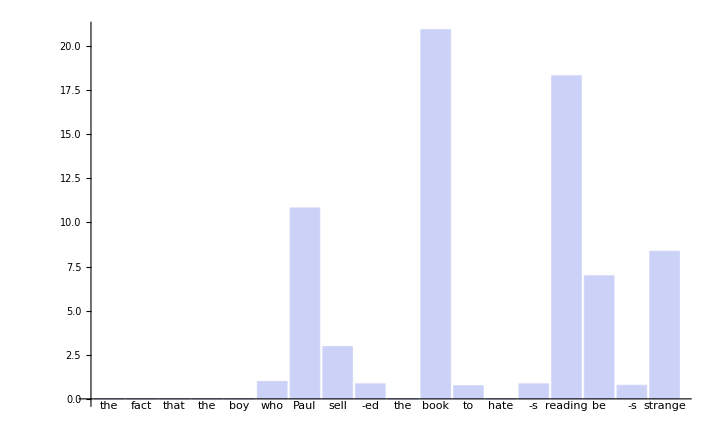

```mathematica
BarChart[entropyreductions[[#]],ChartLabels->keenanhawkins[[#]],ImageSize->72*10]&/@{10}
```

### Word-by-Word Comparison

```mathematica
PairedBarChart[Style[entropyreductions[[#]],Orange],Style[surprisals[[#]],Purple],ImageSize->72*6,ChartLabels->keenanhawkins[[#]]]&/@Range[3,4]
```

{-Graphics-,-Graphics-}